# Analyzing the Changes in Ideology of the Democratic and Republican Party’s Political Parties from 1900 to 2020

## Introduction

Politics have been an essential part of society since the very beginning, shaping the structure of our government and policies, which in turn affect our lives. The importance of politics have also led to a variety of different political thoughts, such as certain beliefs, policies, and ideas. Throughout the world, people and politicians with similar political thoughts and ideologies have come together to form political entities known as political parties. 

In the United States, the two major political parties are the Democratic Party and the Republican Party. These two political parties, which have existed since the 1800s and have often been political rivals in the US government. Currently, the Democratic Party is known to be a left-wing political party while the Republican Party is considered as a right-wing political party.

However, their political ideologies and ideas have undergone significant shifts throughout the years. This begs the question: Can we analyze how the Democratic and Republican parties’ ideologies have shifted throughout the course of US history?

## Gathering the Data

First, I decided to obtain the political party platforms from The American Presidency Project by UC Santa Barbara. Both the Democratic Party and Republican Party publishes a party platform every four years, which is a long document that explains their stances on political issues and values that will guides the party. Since the party platforms is an official description on the ideologies of the two political parties, these were the primary data that were used for analysis. 

The website only included party platforms up to 2020, as this project was created before the Democratic and Republican Conventions of 2024, which is when they publish their party platform. As a result, this project could only use party platforms up to the year 2020. 

For this project, only party platforms between the years 1900 and 2020, inclusive, will be used for analysis. 

The website was a table of political party platforms by presidential election year with a hyperlink to a separate page that featured the party platform.

The code below gets a list of all of the hyperlinks that are in the main page of the list of party platforms. I used a pattern to selected all of the links connected to the Democratic Party Platform.

```mathematica
democrats =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"-democratic-party-platform"], Length[#] > 0 &]];
```

The code below does the same action as the previous code, but collects all of the hyperlinks connected to the Republican Party platforms.

```mathematica
republicans =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"republican-party-platform"~~___], Length[#] > 0 &]];
```

Using the list of hyperlinks that I obtained for each party, I imported the HTML code from each of the pages. Then, I only took the the text that is inside the HTML div tag with the id “field-docs-content”. This is because this div tag contained the content of the web page, which were the party platforms. It also removes all of the HTML tags that are located within the text. 

The code below obtains all of the Democratic Party’s party platforms.

```mathematica
demtexts =StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""], 21;;-1] & /@ democrats[[1;;31]];
```

The code below gathers all of the Republican Party’s party platforms.

```mathematica
reptexts = StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""],21;;-1] & /@ republicans[[2;;31]];
```

This project will not use the 2020 statement from the Republican Party because the party cancelled the 2020 Republican Convention due to the COVID-19 pandemic and the document is an affirmation of the reuse of the 2016 Republican Party platform. As a result, the the 2020 Republican Party platform can be considered as the same as that of 2016.

## Visualizing Party Platforms using Principal Components Analysis

When analyzing similarities between texts and clustering, a large amount of dimensions and features will be used, which leads to many issues such as overfitting, scarcity of data, and the inability to represent more than three dimensions. 

Principal Components Analysis is a way around this issue by reducing the number of dimensions to a set of “principal components” that still captures the most important patterns and maximizes the variance within the data. When using text, vector embedding will be used to convert the text into numbers that describes the characteristics of the text. These numbers will be used in the PCA. 

I decided to use PCA in order to visualize how the Democratic and Republican Parties’ party platforms change by plotting them on a 2-dimensional graph and comparing where they lie. 

The first dimension of the graph would be the first principal component, which captures the most variation, and the second dimension would be the second principal component, which captures the most variance that is orthogonal to the first component. Although what the principal components exactly are will not be discussed in the project, it allows for an abstract visualization of the shifts of the political parties.

### Preprocessing the Data

Using the texts of the party platforms that I had obtained, I decided to create an association where the key was the year and political party and the value was the party platform. This will be used to label the points when we perform the principal components analysis. 

The bottom code creates two associations for Democratic and Republican Party’s platforms and then creates a large association that would include all platforms.

```mathematica
demkeys = Table[StringJoin[ToString[2024 - 4*i], " Democratic Party"], {i, Range[Length[demtexts]]}];
```

```mathematica
democratTexts =Association[Table[demkeys[[i]] -> demtexts[[i]], {i, Range[Length[demtexts]]}]];
```

```mathematica
reptexts = StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""],{21;;-1}] & /@ republicans[[2;;31]];
```

```mathematica
repkeys = Table[StringJoin[ToString[2020 - 4*i], " Republican Party"], {i, Range[Length[reptexts]]}];
```

```mathematica
republicanTexts =Association[Table[repkeys[[i]] -> reptexts[[i]], {i, Range[Length[reptexts]]}]];
```

```mathematica
alltexts = Join[democratTexts, republicanTexts]
```

### Performing Principal Components Analysis on the Party Platforms

The function below returns the color Red if the input ends with “Republican Party” and Blue if the input ends with “Democratic Party”. This is in order to color the points on the graph based on the colors of the political party that the party platform was published by.

```mathematica
partycolors[p_] := If[StringTake[p, 6;;-1]=="Republican Party", Red, Blue]
```

The code below performs principal component analysis on all of the party platforms and plots each of the party platforms on a graph.

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[alltexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[alltexts], Keys[alltexts]}], ImageSize->Full, PlotRangePadding->{10, 100}]]
```

In the graph, it is shown that for both the Democratic and Republican Party, the platforms are generally going chronologically from left to right. However, additionally, although the Republican and Democratic Party are at relatively similar positions in the first half of the 20th century, starting from the 1960s and 1970s, a divide between the two parties becomes increasingly clear. This is especially true in the last 20 years, as seen in the graph, where the Republican Party has started to go increasingly higher while the Democratic Party is going increasingly lower. 

This correlates with the ideological shift between the Republican and Democratic Party during the mid-1900s, when the Democratic Party shifted towards supporting civil rights, which alienated its traditional Southern voters who then moved to the Republican Party. The increasing polarization and partisan nature of American politics during the 21st century was also shown in the drastic separation between the two political parties in the graph. 

I also created two separate graphs that shows only the shift of the Republican Party and Democratic Party.

### Principal Components Analysis on the Republican Party’s Party Platforms.

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[republicanTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[republicanTexts], Keys[republicanTexts]}], ImageSize->Full, PlotRangePadding->{10, 60}]]
```

### Principal Components Analysis on the Democratic Party’s Party Platforms.

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[democratTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[democratTexts], Keys[democratTexts]}], ImageSize->Full, PlotRangePadding->{10, 160}]]
```

One notable exception to the pattern of the shifts of the political parties is the 1984 Democratic Party, which can be shown in the Democratic Party’s graph and the overall graph to be much further away from party platforms from similar time periods. 

The president of the United States during this year was Ronald Reagan, who is known to have transformed the Republican Party and American politics as a whole by becoming the charismatic leader of conservatism and introducing it into mainstream politics. He brought the rise of a new conservative movement in the Republican Party and coupled with his popularity throughout the nation, the Democratic Party may have felt threatened and prompted to be more opposed to the Republican Party than previous years. In fact, the term “Reagan” appears 197 terms in the party platform for that year, referencing an member of the opposing party much more than other party platforms during this time. In the end, the Democratic nominee for that year, Walter Mondale, ended up losing in a massive landslide against Reagan.

## How the Party Platforms Change Based on Specific Issues and Content

Unfortunately, solely using principle components analysis on the party platforms does not give the actually ways or reasons why the sudden separation in the graph occurred. Although it can be inferred that it is due to the increasing polarization of American politics, it cannot be proven by the dimension reduction alone. 

As a result, natural language processing can be used to determine in what specific ways the party platforms are different.

### Word count of the Opposing Party’s Nominee

First, the word count of the opposing party’s nominee of that year’s election in the party platform can be used to determine the degree of ___

```mathematica
republicanNominee = {"Trump","Trump","Romney","McCain","Bush","Bush","Dole","Bush","Bush","Reagan","Reagan","Ford","Nixon","Nixon","Goldwater","Nixon","Eisenhower","Eisenhower","Dewey","Dewey","Willkie","Landon","Hoover","Hoover","Coolidge","Harding","Hughes","Taft","Taft","Roosevelt","McKinley"};
```

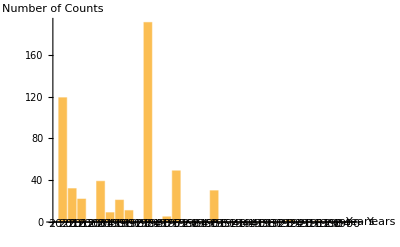

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[democratTexts], republicanNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[democratTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
democratNominee = {"Clinton", "Obama", "Obama", "Kerry", "Gore", "Clinton", "Clinton", "Dukakis", "Mondale", "Carter", "Carter", "McGovern", "Humphrey", "Johnson", "Kennedy", "Stevenson","Stevenson", "Truman", "Roosevelt", "Roosevelt", "Roosevelt", "Roosevelt", "Smith", "Davis", "Cox", "Wilson", "Wilson", "Bryan", "Parker", "Bryan"};
```

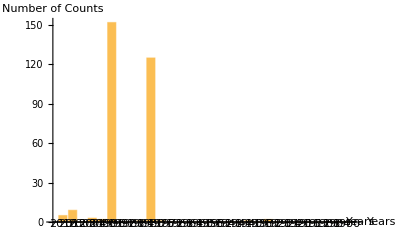

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[republicanTexts], democratNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[republicanTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

Neutral/Partisan classification

```mathematica
neutPart = Import["/Users/eugenehwang/Work/WSRP2024_Eugene_Hwang/political_social_media.csv", "Data", HeaderLines->1]
```

```mathematica
classNeutPart = Table[StringReplace[ToString[s[[21]]], PunctuationCharacter:>""]->s[[8]], {s, neutPart}]
```

```mathematica
demPartisanCount = Mean[Table[ps["partisan"],{ps, libconsf[TextSentences[#],"Probabilities"]}]]& /@ Values[democratTexts]
```

{0.703211,0.696444,0.658335,0.654036,0.598425,0.647225,0.664165,0.598313,0.720076,0.698671,0.641517,0.710451,0.722308,0.600104,0.620425,0.671227,0.699819,0.599839,0.62437,0.557367,0.692662,0.616512,0.706971,0.734935,0.703282,0.715068,0.710106,0.786173,0.786319,0.806267,0.79256}

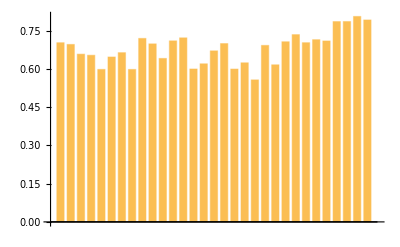

```mathematica
BarChart[demPartisanCount]
```

```mathematica
repPartisanCount = Mean[Table[ps["partisan"],{ps, libconsf[TextSentences[#],"Probabilities"]}]]& /@ Values[republicanTexts]
```

{0.708057,0.684293,0.65792,0.567213,0.663928,0.689252,0.658059,0.631696,0.63709,0.703443,0.669713,0.622125,0.622125,0.696871,0.632323,0.590069,0.717187,0.643967,0.662785,0.74188,0.675587,0.708868,0.68367,0.705545,0.782417,0.813895,0.746157,0.711108,0.741839,0.668466}

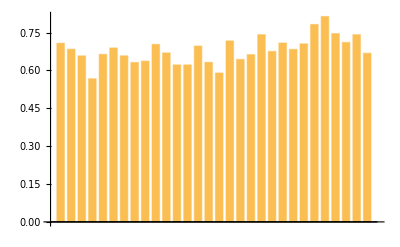

```mathematica
BarChart[repPartisanCount]
```

Clustering and finding topics in similar party platforms in Democrat and Republican Parties

```mathematica
umapDem = DimensionReduce[Values[democratTexts], FeatureExtractor -> "WordVectors",Method->"UMAP"]
```

{{-2.67434,6.08254},{-2.31095,5.99286},{-3.54602,6.07275},{-4.8112,4.91323},{-3.34861,4.21233},{-4.39267,5.6556},{-4.71054,4.38124},{-2.14425,4.67019},{0.660192,4.70708},{-3.37618,3.56226},{-1.10703,2.64129},{-0.0174895,3.45551},{-2.54372,3.08079},{0.087519,3.77646},{-0.769468,2.95153},{-1.50055,5.19417},{-0.24778,6.07957},{-0.168869,5.85772},{2.27748,5.33726},{4.58389,7.09443},{1.90248,5.10051},{2.81487,5.67868},{4.08627,6.34178},{1.85527,8.52152},{1.56304,7.18014},{3.12836,8.97117},{4.3179,8.45497},{2.00323,8.45381},{3.50569,8.81481},{3.15741,7.60167},{4.61102,7.4387}}

```mathematica
demClusters =FindClusters[umapDem, Method->"DBSCAN"];
```

```mathematica
labeledDemClusters = Table[Table[c->Keys[democratTexts][[Position[umapDem, c][[1]][[1]]]], {c, lst}], {lst, demClusters}];
```

```mathematica
ListPlot[labeledDemClusters, ImageSize->Large, PlotLegends->Automatic]
```

-Graphics-

```mathematica
textWordsDem = Join[WordStem /@TextWords[StringJoin[Table[StringDelete[StringReplace[DeleteStopwords[ToLowerCase[democratTexts[y]]], PunctuationCharacter :>""], DigitCharacter..], {y, Values[#]}]]]]& /@ labeledDemClusters;
```

```mathematica
demWordTF =Reverse[SortBy[Table[{w[[1]], w[[2]]/Length[#]}, {w,N[Tally[#]]}], Last]] & /@ textWordsDem
```

```mathematica
demWordIDF = Table[{w[[1]],Log[N[Length[textWordsDem]/Length[Select[textWordsDem, MemberQ[#, w[[1]]] &]]]]}, {w, #}] &/@demWordTF
```

```mathematica
tfidfDem = Join[{"Cluster: " ~~ToString[#]},Select[Reverse[SortBy[Table[{demWordTF[[#]][[i]][[1]], demWordTF[[#]][[i]][[2]] * demWordIDF[[#]][[i]][[2]]}, {i, Range[Length[demWordTF[[#]]]]}], Last]], ResourceFunction["NounQ"][#[[1]]] &,10][[All,1]]] & /@ Range[Length[demWordTF]];
```

```mathematica
Grid[tfidfDem, Frame->All]
```

Cluster: 1 | program | bush | help | job | health | communist | access | atom | drug | research
Cluster: 2 | trump | gore | student | health | job | help | access | internet | drug | clean
Cluster: 3 | telegraph | raiser | battleship | c | toil | rascal | favor | express | tariff | b
Cluster: 4 | pulp | speaker | favor | panic | medium | workingman | exhibit | port | prison | render
Cluster: 5 | job | bush | drug | health | environment | soviet | program | help | john | cut
Cluster: 6 | program | soviet | percent | carter | health | job | goal | implement | help | student
Cluster: 7 | silver | liquor | plea | plank | paper | uplift | temper | saloon | imperialist | freemen
Cluster: 8 | passport | frame | sailor | woe | weal | truce | trammel | spectacular | sharer | proverb
Cluster: 9 | program | atom | stunt | help | soviet | communist | health | brotherhood | bluster | goal
Cluster: 10 | program | youth | implement | health | leadership | chart | million | wheat | radio | launch
Cluster: 11 | environment | drug | help | revers | homeless | coast | health | weapon | soviet | partnership
Cluster: 12 | shoal | barter | taint | referendum | cordial | leas | toiler | slaughter | p | flat

```mathematica
umapRep = DimensionReduce[Values[republicanTexts], FeatureExtractor -> "WordVectors",Method->"UMAP"]
```

{{25.6005,8.16344},{26.456,8.27596},{27.6307,6.78995},{25.7967,6.50091},{27.6511,5.84632},{27.5523,5.86485},{27.1627,7.71421},{26.1919,4.43929},{26.6833,4.76299},{27.6899,6.84113},{24.7256,6.58145},{23.5703,7.2307},{22.6305,5.79721},{23.3335,6.36765},{22.2662,7.85435},{21.5667,5.88485},{21.3422,8.31927},{18.5446,10.3426},{20.8445,7.94347},{19.6629,10.0966},{20.691,9.26773},{18.6053,6.58704},{19.9146,6.40499},{19.6849,8.02377},{20.5306,6.6678},{16.783,8.84603},{18.0186,7.71346},{18.2047,7.47153},{16.9133,9.08465},{18.0821,9.38669}}

```mathematica
repClusters =FindClusters[umapRep, Method->"DBSCAN"];
```

```mathematica
labeledRepClusters = Table[Table[c->Keys[republicanTexts][[Position[umapRep, c][[1]][[1]]]], {c, lst}], {lst, repClusters}]
```

{{{16.783,8.84603}→1916 Republican Party,{16.9133,9.08465}→1904 Republican Party,{18.0821,9.38669}→1900 Republican Party},{{22.2662,7.85435}→1960 Republican Party,{21.3422,8.31927}→1952 Republican Party,{20.8445,7.94347}→1944 Republican Party,{19.6849,8.02377}→1924 Republican Party},{{18.5446,10.3426}→1948 Republican Party,{19.6629,10.0966}→1940 Republican Party},{{25.7967,6.50091}→2004 Republican Party,{24.7256,6.58145}→1976 Republican Party,{22.6305,5.79721}→1968 Republican Party,{23.3335,6.36765}→1964 Republican Party,{21.5667,5.88485}→1956 Republican Party},{{27.6511,5.84632}→2000 Republican Party,{27.5523,5.86485}→1996 Republican Party},{{27.6307,6.78995}→2008 Republican Party,{27.6899,6.84113}→1980 Republican Party},{{23.5703,7.2307}→1972 Republican Party},{{18.0186,7.71346}→1912 Republican Party,{18.2047,7.47153}→1908 Republican Party},{{18.6053,6.58704}→1932 Republican Party,{19.9146,6.40499}→1928 Republican Party,{20.5306,6.6678}→1920 Republican Party},{{26.1919,4.43929}→1988 Republican Party,{26.6833,4.76299}→1984 Republican Party},{{20.691,9.26773}→1936 Republican Party},{{25.6005,8.16344}→2016 Republican Party,{26.456,8.27596}→2012 Republican Party,{27.1627,7.71421}→1992 Republican Party}}

```mathematica
ListPlot[labeledRepClusters, ImageSize->Large, PlotLegends->Automatic]
```

-Graphics-

```mathematica
textWordsRep= Join[WordStem /@TextWords[StringJoin[Table[StringDelete[StringReplace[DeleteStopwords[ToLowerCase[republicanTexts[y]]], PunctuationCharacter :>""], DigitCharacter..], {y, Values[#]}]]]]& /@ labeledRepClusters;
```

```mathematica
repWordTF =Reverse[SortBy[Table[{w[[1]], w[[2]]/Length[#]}, {w,N[Tally[#]]}], Last]] & /@ textWordsRep
```

```mathematica
repWordIDF = Table[{w[[1]],Log[N[Length[textWordsRep]/Length[Select[textWordsRep, MemberQ[#, w[[1]]] &]]]]}, {w, #}] &/@repWordTF
```

```mathematica
tfidfRep = Join[{"Cluster: "~~ToString[#]},Select[Reverse[SortBy[Table[{repWordTF[[#]][[i]][[1]], repWordTF[[#]][[i]][[2]] * repWordIDF[[#]][[i]][[2]]}, {i, Range[Length[repWordTF[[#]]]]}], Last]], ResourceFunction["NounQ"][#[[1]]] &,10][[All,1]]] & /@ Range[Length[repWordTF]];
```

```mathematica
Grid[tfidfRep, Frame->All]
```

Cluster: 1 | cordial | statesman | tender | countrymen | gold | statesmanship | sailor | neutral | earnest | upright
Cluster: 2 | program | annum | communist | atom | help | research | leadership | progress | growth | assist
Cluster: 3 | teamwork | mob | brotherhood | whirl | treason | rearmament | incident | hoof | descent | column
Cluster: 4 | bush | terrorist | help | terror | program | access | percent | leadership | job | goal
Cluster: 5 | dole | bob | access | bush | environment | bill | governor | agenda | role | percent
Cluster: 6 | carter | soviet | access | percent | program | job | neighborhood | role | growth | goal
Cluster: 7 | program | help | leadership | addition | job | young | passport | poor | soviet | train
Cluster: 8 | session | firemen | derelict | telegraph | seamen | panic | statesmanship | militia | domain | writ
Cluster: 9 | eighteenth | discount | coven | comfort | congressmen | leadership | bank | debtor | earnest | railroad
Cluster: 10 | soviet | percent | program | parent | job | ranch | help | s | drug | growth
Cluster: 11 | dishonor | autocrat | sweatshop | purport | protector | fright | wild | tender | swarm | coin
Cluster: 12 | bush | access | job | abort | like | current | internet | environment | parent | student

## Conclusion

## Future Work

## References

https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3
https://christopherwolfram.com/projects/dimensionality-of-politics/
https://www.britannica.com/topic/political-spectrum
https://www.britannica.com/topic/Democratic-Party
https://www.britannica.com/topic/Republican-Party
https://www.reaganlibrary.gov/reagans/reagan-administration/reagan-presidency
https://www.geeksforgeeks.org/principal-component-analysis-pca/
https://williamjturkel.net/2012/11/19/basic-text-analysis-in-mathematica/ 
https://towardsdatascience.com/text-vectorization-term-frequency-inverse-document-frequency-tfidf-5a3f9604da6d

## Acknowledgements

I would like to thank my mentor, Jack Heseltime, and my teacher’s assistant, Nicoló Monti for their infinite patience, their constant assistance throughout this project, and their willingness to guide me through my first ever research project.

## Cite this Notebook